```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

## System Description

The system consists of two individual thermal transistors T_1 and T_2, connected in a Darlington pair configuration. The thermal flow between T_1 and T_2 is mediated via an intermediate energy divider mechanism. 
T_1 - Connected to two thermal baths, B_HOT (collector), B_CNT (base) and emitter connected to the HIGH side of the energy divider
T_2 - Connected to two thermal baths, B_HOT (collector), B_COL (emitter) and base connected to the LOW side of the energy divider

The thermal bath B_HOT is at a high temperature, while B_COL is at a low temperature. The temperature T_CNT of control terminal  B_CNT can be varied.
The energy divider mechanism receives and transmits energy to the two transistors.

Each transistor is modelled individually using the techniques developed for Optically Controlled Quantum Thermal Gate paper. However, we use a simplified 4×4 density matrix model instead of the previous 8×8 model. This is only valid under the conditions
	1. ω_L^S=ω_M^S=ω_R^S = 0
	2. ω_RL^S=0

The main reason for this is simplicity. Under a N-level energy divider and 8-level transistor model, we would have a 8×8×N = 64N dimensional vector space. This reduces to a 4×4×N = 16N level space under a 4-level transistor model.

The previous transistor eigenstates group together in groups of 2,
|1> = |+z,+z,+z> = |-z,-z,-z>
|2> = |+z,+z,-z> = |-z,-z,+z>
|3> =|+z,-z,+z> = |-z,+z,-z> 
|4> =|+z,-z,-z> = |-z,+z,+z>

## Energy divider parameters

N is the total number of quantum states in the intermediate energy divider.
p is the number of jumps in the HIGH side.
q is the number of jumps in the LOW side.
This makes a q/p energy divider.

```mathematica
Ns=3;p=2;q=1;
```

```mathematica
Ns=4;p=3;q=1;
```

```mathematica
Ns=5;p=3;q=2;
```

The intermediate energy divider regulates the energy flow between the |3_T_1>↔|4_T_1> transition of the first transistor, and the |2_T_2><->|4_T_2> transition of the second transistor.
However, the|2_T_1>↔|1_T_1> transition of the first transistor, needs also be considered since they have the same transition frequency as the |3_T_1>↔|4_T_1> transition.

To properly match the energy levels in the HIGH and LOW sides, we need the conditions,
	1. ω_MR^T_1≃p ω_ED
	2. ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
where ℏ ω_ED is the energy of the intermediate harmonic oscillator.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

The system contains three subsystems T_1, T_2 and T_ED. 
T_1 and T_2 are thermal transistors modelled as 4-level systems. T_ED is a harmonic oscillator truncated at N levels.

#### Transistor Hamiltonian

Transistor Hamiltonian consists of two parts,
	1) The first part consists of the ultrastrong coupling between the three TLSs

```mathematica
HsT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 1]-Subscript[ωMR, 1]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 1]+Subscript[ωMR, 1]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 1]+Subscript[ωMR, 1])}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HsT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0, 0, 0}, {0, 1/2 ℏ (Subscript[ωLM, 2]-Subscript[ωMR, 2]), 0, 0}, {0, 0, -1/2 ℏ (Subscript[ωLM, 2]+Subscript[ωMR, 2]), 0}, {0, 0, 0, 1/2 ℏ (-Subscript[ωLM, 2]+Subscript[ωMR, 2])}})[[veT2,hoT2]]
```

2) The second part consists of the field interactions with the external, tuned, electromagnetic field. The Hamiltonian below is given in its Schrodinger picture representation.

```mathematica
HlT1Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 1])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 1]-Subscript[ωMR, 1])), 0, 0}})[[veT1,hoT1]]Id[veED,hoED]Id[veT2,hoT2]
HlT2Sep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1]Id[veED,hoED]({{0, 0, 0, 0}, {0, 0, 0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(-ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2]))}, {0, 0, 0, 0}, {0, -(ℏ Subscript[Ω, 2])/2 ⅇ^(+ⅈ t (Subscript[ωLM, 2]-Subscript[ωMR, 2])), 0, 0}})[[veT2,hoT2]]
```

#### Energy divider Hamiltonian

```mathematica
Table[ℏ ωED(Ns-veED)veED,hoED,{veED,1,Ns},{hoED,1,Ns}]//MatrixForm
```

(2 ωED ℏ | 0 | 0
0 | ωED ℏ | 0
0 | 0 | 0)

```mathematica
HsEDSep[veT1_,hoT1_,veED_,hoED_,veT2_,hoT2_]:=Id[veT1,hoT1](ℏ ωED(Ns-veED)veED,hoED)Id[veT2,hoT2]
```

### Forming the combined system Hamiltonian

The total number of combined system eigenstates are 4×N×4 = 16N.

In the matrix representation, we enumerate the energy levels as |(state of T_1) + (state of T_ED)+(state of T_2)>

the highest energy state |e,N,e> is given the first place, and the lowest energy state |g,0,g> is given the last space. 

For example,
|1>	= |1,N-1,1>
|2>	= |1,N-1,2>
|3>	= |1,N-1,3>
|4>	= |1,N-1,4>
|5> 	= |1,N-2,1>
|6> 	= |1,N-2,2>
....
|16N-3>	= |4,0,1>
|16N-2>	= |4,0,2>
|16N-1>	= |4,0,3>
|16N> 	= |4,0,4>

Eigenstate mapping function, maps overall state (1 to 16N) to subsystem T_1, T_ED, T_2 state,

```mathematica
EmapT1[i_]:=Quotient[i-1,4Ns]+1
EmapED[i_]:=Quotient[QuotientRemainder[i-1,4Ns][[2]],4]+1
EmapT2[i_]:=QuotientRemainder[i-1,4][[2]]+1
```

```mathematica
Table[EmapT1[i],{i,1,16Ns}]
Table[EmapED[i],{i,1,16Ns}]
Table[EmapT2[i],{i,1,16Ns}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4}

{1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3,1,1,1,1,2,2,2,2,3,3,3,3}

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}

Matrix form of the three Hamiltonians

```mathematica
HsT1[ve_,ho_]:=HsT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsED[ve_,ho_]:=HsEDSep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HsT2[ve_,ho_]:=HsT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]

HlT1[ve_,ho_]:=HlT1Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
HlT2[ve_,ho_]:=HlT2Sep[EmapT1[ve],EmapT1[ho],EmapED[ve],EmapED[ho],EmapT2[ve],EmapT2[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space (We consider the field interaction (Ĥ)_(field-sys)^S as a perturbation. Hence it is not included here, but in the Hsys1Matrix.

```mathematica
Hsys0Matrix = Table[HsT1[ve,ho]+HsED[ve,ho]+HsT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];

Hsys0EVal[i_]:=Diagonal[Hsys0Matrix][[i]]
Diagonal[Hsys0Matrix]//MatrixForm
```

(2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2)
1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Interaction Hamiltonian between the subsystems

The interactions between the subsystems are considered WEAK enough such that the local master equation approach is justified.
This effectively means that the subsystem interactions should not significantly change the energy levels of the non-interacting, subsystem Hamiltonians.

The energy levels of the individual components are specially tuned in our model. 
	1. First of all, there are no direct interactions between T_1 and T_2.
	2. The energy levels are prepared so that
		ω_MR^T_1≃p ω_ED
		ω_MR^T_2-ω_LM^T_2 ≃q ω_ED
	3. Therefore the interactions are such that
		a) T_1 jumps up from |3_T_1> to |4_T_1> (or |2_T_1> to |1_T_1> ) while the HO jumps down p steps from |(m+p)_T_ED> to |m_T_ED> (and vice versa).
		b) T_2 jumps up from |2_T_2> to |4_T_2> while the HO jumps down q steps from |(m+q)_T_ED> to |m_T_ED> (and vice versa).
	3. The interaction strengths between subsystems are given by γ_T_1[m] and γ_T_2[m] with m enumerating the different start (or end) state of the HO.

First define some necessary matrices

```mathematica
OneMatrix[ve_,ho_,n_]:=Table[ve,i ho,j,{i,1,n},{j,1,n}]
{{OneMatrix[Ns-m,Ns-(m+p),Ns]/.m->0//MatrixForm,OneMatrix[Ns-(m+p),Ns-m,Ns]/.m->0//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->0//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->0//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->1//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->1//MatrixForm},
{OneMatrix[Ns-m,Ns-(m+q),Ns]/.m->2//MatrixForm,OneMatrix[Ns-(m+q),Ns-m,Ns]/.m->2//MatrixForm}}
```

{{(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)},{(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0),(0 | 0 | 0
0 | 0 | 1
0 | 0 | 0)},{(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0)},{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}}

Considering the above Hamiltonian, we write the interaction between T_1 and T_ED as,

```mathematica
HintT1andED[ve_,ho_]:=(∑_(m=0)^(Ns-1-p) (ℏ γT1[m]KroneckerProduct[(KroneckerProduct[({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}}),OneMatrix[Ns-m,Ns-(m+p),Ns]]+KroneckerProduct[({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),OneMatrix[Ns-(m+p),Ns-m,Ns]]),IdentityMatrix[4]]))[[ve,ho]]
```

Similarly, we write the interaction between T_ED and T_2 as,

```mathematica
HintEDandT2[ve_,ho_]:=(∑_(m=0)^(Ns-1-q) (ℏ γT2[m]KroneckerProduct[IdentityMatrix[4],(KroneckerProduct[OneMatrix[Ns-m,Ns-(m+q),Ns],({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}})]+KroneckerProduct[OneMatrix[Ns-(m+q),Ns-m,Ns],({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})])]))[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix = Table[HintT1andED[ve,ho]+HintEDandT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys2Matrix = Table[HlT1[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
Hsys3Matrix = Table[HlT2[ve,ho],{ve,1,16Ns},{ho,1,16Ns}];
{MatrixForm[Hsys1Matrix],MatrixForm[Hsys2Matrix],MatrixForm[Hsys3Matrix]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0)}

## Combined system Hamiltonian

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix+Hsys2Matrix+Hsys3Matrix;
MatrixForm[HsysMatrix]
```

(2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (ωLM_1-ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ-1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | -1/2 ℏ (ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 2 ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | ωED ℏ+1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2+ωMR_2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (ωLM_2-ωMR_2) | 0 | -1/2 ⅇ^(-ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)-1/2 ℏ (ωLM_2+ωMR_2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_1-ωMR_1)) ℏ Ω_1 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -1/2 ⅇ^(ⅈ t (ωLM_2-ωMR_2)) ℏ Ω_2 | 0 | 1/2 ℏ (-ωLM_1+ωMR_1)+1/2 ℏ (-ωLM_2+ωMR_2))

## Density Matrix

In the combined system, the density matrix is 12×12.

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,16Ns},{ho,1,16Ns}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(1)
 |  |  |  |

## System-bath interactions

The inter-subsystem interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystems of the individual subsystems are minimally affected by this interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual transistor Hamiltonians.

### Thermal interactions of individual transistors

In the simplified individual transistor model, each bath has two Lindblad operators

```mathematica
Subscript[LinOps, S_,P_][i_]:=({{({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}})}, {({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})}})[[P,i]]
Subscript[ωLinOps, S_,P_][i_]:=({{-Subscript[ωLM, S], -Subscript[ωLM, S]}, {-Subscript[ωLM, S]-Subscript[ωMR, S], -Subscript[ωLM, S]+Subscript[ωMR, S]}, {-Subscript[ωMR, S], Subscript[ωMR, S]}})[[P,i]]
```

### Interactions of the hot bath B_HOT

B_HOT is connected to the collectors of both T_1 and T_2. Hence, we need to extract the S=1, P=1 and S=2, P=1 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BHOT[i_]:=KroneckerProduct[Subscript[LinOps, 1,1][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BHOT[i_]:=Subscript[ωLinOps, 1,1][i]
AMatrixT2BHOT[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,1][i]]]
ωT2BHOT[i_]:=Subscript[ωLinOps, 2,1][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BHOT[i]],{i,1,2}];
Table[MatrixForm[AMatrixT2BHOT[i]],{i,1,2}];
Table[MatrixForm[ωT1BHOT[i]],{i,1,2}]
Table[MatrixForm[ωT2BHOT[i]],{i,1,2}]
```

{-ωLM_1,-ωLM_1}

{-ωLM_2,-ωLM_2}

### Interactions of the control bath B_CNT

B_CNT is connected to the base of T_1. Hence, we need to extract the S=1, P=2 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT1BCNT[i_]:=KroneckerProduct[Subscript[LinOps, 1,2][i],KroneckerProduct[IdentityMatrix[Ns],IdentityMatrix[4]]]
ωT1BCNT[i_]:=Subscript[ωLinOps, 1,2][i]
```

```mathematica
Table[MatrixForm[AMatrixT1BCNT[i]],{i,1,2}];
Table[MatrixForm[ωT1BCNT[i]],{i,1,2}]
```

{-ωLM_1-ωMR_1,-ωLM_1+ωMR_1}

### Interactions of the cold bath B_COL

B_COL is connected to the emitter of T_2. Hence, we need to extract the S=2, P=3 Lindblad operators. To convert to the full 16N space, we need to expand the operators using proper identity matrices.

```mathematica
AMatrixT2BCOL[i_]:=KroneckerProduct[IdentityMatrix[4],KroneckerProduct[IdentityMatrix[Ns],Subscript[LinOps, 2,3][i]]]
ωT2BCOL[i_]:=Subscript[ωLinOps, 2,3][i]
```

```mathematica
Table[MatrixForm[AMatrixT2BCOL[i]],{i,1,2}];
Table[MatrixForm[ωT2BCOL[i]],{i,1,2}]
```

{-ωMR_2,ωMR_2}

### Lindblad terms of the master equation

```mathematica
LinTerm[ρ_,A_,J_,NBE_,ω_]:=∑_(i=1)^2 (J[ω[i]](1+NBE[ω[i]])(A[i].ρ.A[i]†-1/2(A[i]†.A[i].ρ+ρ.A[i]†.A[i]))+J[ω[i]]NBE[ω[i]](A[i]†.ρ.A[i]-1/2(A[i].A[i]†.ρ+ρ.A[i].A[i]†)))
```

```mathematica
LinMatrixT1BHOT[ρ_]:=LinMatrixT1BHOT[ρ]=LinTerm[ρ,AMatrixT1BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT1BHOT]
LinMatrixT2BHOT[ρ_]:=LinMatrixT2BHOT[ρ]=LinTerm[ρ,AMatrixT2BHOT,Subscript[J, 1],Subscript[NBE, 1],ωT2BHOT]
LinMatrixT1BCNT[ρ_]:=LinMatrixT1BCNT[ρ]=LinTerm[ρ,AMatrixT1BCNT,Subscript[J, 2],Subscript[NBE, 2],ωT1BCNT]
LinMatrixT2BCOL[ρ_]:=LinMatrixT2BCOL[ρ]=LinTerm[ρ,AMatrixT2BCOL,Subscript[J, 3],Subscript[NBE, 3],ωT2BCOL]
```

```mathematica
MatrixForm[Simplify[LinMatrixT1BHOT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT2BHOT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT1BCNT[ρMatrix[t]]]]
MatrixForm[Simplify[LinMatrixT2BCOL[ρMatrix[t]]]]
```

(1)
 |  |  |  |

(1)
 |  |  |  |

(1)
 |  |  |  |

«1 more identical outputs»

## Defining the interaction picture

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys2INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys2Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
Hsys3INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys3Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
MatrixForm[Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ⅇ^(ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ⅇ^(-ⅈ t (2 ωED-ωMR_1)) ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ t (ωED+ωLM_2-ωMR_2)) ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0)

Simplify the Hamiltonian for the fully resonant case,

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
Hsys2INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys2Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
Hsys3INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys3Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]//.{ωED->Subscript[ωMR, 1]/p,Subscript[ωMR, 1]->p/q(Subscript[ωMR, 2]-Subscript[ωLM, 2])}];
MatrixForm[Hsys1INTMatrix+Hsys2INTMatrix+Hsys3INTMatrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT1[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | ℏ γT2[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[1] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_2)/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ Ω_1)/2 | 0 | 0 | 0 | ℏ γT1[0] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ γT2[0] | 0 | 0 | 0 | -(ℏ Ω_2)/2 | 0 | 0)

## Quantum Markovian master equation

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHSengdiv=-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix);
Subscript[RHSfield, 1]=-ⅈ/ℏ(Hsys2INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys2INTMatrix);
Subscript[RHSfield, 2]=-ⅈ/ℏ(Hsys3INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys3INTMatrix);
```

```mathematica
RHS=RHSengdiv+Subscript[RHSfield, 1]+Subscript[RHSfield, 2]+LinMatrixT1BHOT[ρMatrix[t]]+LinMatrixT2BHOT[ρMatrix[t]]+LinMatrixT1BCNT[ρMatrix[t]]+LinMatrixT2BCOL[ρMatrix[t]];
RHS=Collect[RHS,Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&];
```

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(1)
 |  |  |  |

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,16Ns},{j,1,16Ns}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[{Table[{Subscript[J, P][ω_]},{P,1,3}],Subscript[Ω, 1],Subscript[Ω, 2],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]]]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;(16Ns+1)]];
soloffdiag=Delete[sol,Table[{1+(16Ns+1)i},{i,0,(16Ns-1)}]];
```

Net thermal decaying rate Τ_(S,P)[i,j] of component S from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_(S,P)[i,j] is used due to variable naming issues.

```mathematica
Subscript[ω, i_,j_]:=Simplify[1/ℏ(Hsys0EVal[i]-Hsys0EVal[j])]
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][Subscript[ω, i,j]]((1+Subscript[NBE, P][Subscript[ω, i,j]])Subscript[ρ, i,i][t]-Subscript[NBE, P][Subscript[ω, i,j]]Subscript[ρ, j,j][t])
Subscript[Τsm, P_][i_,j_]:=Subscript[J, P][Subscript[ω, i,j]](Subscript[NBE, P][Subscript[ω, i,j]]Subscript[ρ, j,j][t]+(-1-Subscript[NBE, P][Subscript[ω, i,j]])Subscript[ρ, i,i][t])
```

Net optical field induced decaying rate Υ_P[i,j] of the device P from state | i > to state | j > while absorbing energy from the external electric field.
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[Υs, S_][i_,j_]:= Subscript[Ω, S](1/2 ⅈ Subscript[ρ, i,j][t]-1/2 ⅈ Subscript[ρ, j,i][t])
```

Diagonal equations in simplified form

```mathematica
soldiag/.Flatten[{Table[Subscript[Τs, P][i,j]->Subscript[Τ, P][i,j] ,{P,1,3},{i,1,16Ns},{j,1,16Ns}],Table[Subscript[Τsm, P][i,j]->-Subscript[Τ, P][i,j] ,{P,1,3},{i,1,16Ns},{j,1,16Ns}],Table[Subscript[Υs, S][i,j]->Subscript[Υ, S][i,j] ,{S,1,2},{i,1,16Ns},{j,1,i-1}],Table[Subscript[Υs, S][i,j]->Subscript[Υ, S][i,j] ,{S,1,2},{j,1,16Ns},{i,1,j-1}]}];
%//MatrixForm
```

(ρ_(1,1)'[t]==Τ_1[4,1]+Τ_1[37,1]+Τ_2[25,1]+Τ_3[2,1]
ρ_(2,2)'[t]==Τ_1[3,2]+Τ_1[38,2]+Τ_2[26,2]-Τ_3[2,1]+Υ_2[4,2]+γT2[1] (ⅈ ρ_(2,8)[t]-ⅈ ρ_(8,2)[t])
ρ_(3,3)'[t]==-Τ_1[3,2]+Τ_1[39,3]+Τ_2[27,3]+Τ_3[4,3]
ρ_(4,4)'[t]==-Τ_1[4,1]+Τ_1[40,4]+Τ_2[28,4]-Τ_3[4,3]+Υ_2[2,4]
ρ_(5,5)'[t]==Τ_1[8,5]+Τ_1[41,5]+Τ_2[29,5]+Τ_3[6,5]
ρ_(6,6)'[t]==Τ_1[7,6]+Τ_1[42,6]+Τ_2[30,6]-Τ_3[6,5]+Υ_2[8,6]+γT2[0] (ⅈ ρ_(6,12)[t]-ⅈ ρ_(12,6)[t])
ρ_(7,7)'[t]==-Τ_1[7,6]+Τ_1[43,7]+Τ_2[31,7]+Τ_3[8,7]
ρ_(8,8)'[t]==-Τ_1[8,5]+Τ_1[44,8]+Τ_2[32,8]-Τ_3[8,7]+Υ_2[6,8]+γT2[1] (-ⅈ ρ_(2,8)[t]+ⅈ ρ_(8,2)[t])
ρ_(9,9)'[t]==Τ_1[12,9]+Τ_1[45,9]+Τ_2[33,9]+Τ_3[10,9]+γT1[0] (ⅈ ρ_(9,13)[t]-ⅈ ρ_(13,9)[t])
ρ_(10,10)'[t]==Τ_1[11,10]+Τ_1[46,10]+Τ_2[34,10]-Τ_3[10,9]+Υ_2[12,10]+γT1[0] (ⅈ ρ_(10,14)[t]-ⅈ ρ_(14,10)[t])
ρ_(11,11)'[t]==-Τ_1[11,10]+Τ_1[47,11]+Τ_2[35,11]+Τ_3[12,11]+γT1[0] (ⅈ ρ_(11,15)[t]-ⅈ ρ_(15,11)[t])
ρ_(12,12)'[t]==-Τ_1[12,9]+Τ_1[48,12]+Τ_2[36,12]-Τ_3[12,11]+Υ_2[10,12]+γT2[0] (-ⅈ ρ_(6,12)[t]+ⅈ ρ_(12,6)[t])+γT1[0] (ⅈ ρ_(12,16)[t]-ⅈ ρ_(16,12)[t])
ρ_(13,13)'[t]==Τ_1[16,13]+Τ_1[25,13]+Τ_2[37,13]+Τ_3[14,13]+Υ_1[37,13]+γT1[0] (-ⅈ ρ_(9,13)[t]+ⅈ ρ_(13,9)[t])
ρ_(14,14)'[t]==Τ_1[15,14]+Τ_1[26,14]+Τ_2[38,14]-Τ_3[14,13]+Υ_1[38,14]+Υ_2[16,14]+γT1[0] (-ⅈ ρ_(10,14)[t]+ⅈ ρ_(14,10)[t])+γT2[1] (ⅈ ρ_(14,20)[t]-ⅈ ρ_(20,14)[t])
ρ_(15,15)'[t]==-Τ_1[15,14]+Τ_1[27,15]+Τ_2[39,15]+Τ_3[16,15]+Υ_1[39,15]+γT1[0] (-ⅈ ρ_(11,15)[t]+ⅈ ρ_(15,11)[t])
ρ_(16,16)'[t]==-Τ_1[16,13]+Τ_1[28,16]+Τ_2[40,16]-Τ_3[16,15]+Υ_1[40,16]+Υ_2[14,16]+γT1[0] (-ⅈ ρ_(12,16)[t]+ⅈ ρ_(16,12)[t])
ρ_(17,17)'[t]==Τ_1[20,17]+Τ_1[29,17]+Τ_2[41,17]+Τ_3[18,17]+Υ_1[41,17]
ρ_(18,18)'[t]==Τ_1[19,18]+Τ_1[30,18]+Τ_2[42,18]-Τ_3[18,17]+Υ_1[42,18]+Υ_2[20,18]+γT2[0] (ⅈ ρ_(18,24)[t]-ⅈ ρ_(24,18)[t])
ρ_(19,19)'[t]==-Τ_1[19,18]+Τ_1[31,19]+Τ_2[43,19]+Τ_3[20,19]+Υ_1[43,19]
ρ_(20,20)'[t]==-Τ_1[20,17]+Τ_1[32,20]+Τ_2[44,20]-Τ_3[20,19]+Υ_1[44,20]+Υ_2[18,20]+γT2[1] (-ⅈ ρ_(14,20)[t]+ⅈ ρ_(20,14)[t])
ρ_(21,21)'[t]==Τ_1[24,21]+Τ_1[33,21]+Τ_2[45,21]+Τ_3[22,21]+Υ_1[45,21]
ρ_(22,22)'[t]==Τ_1[23,22]+Τ_1[34,22]+Τ_2[46,22]-Τ_3[22,21]+Υ_1[46,22]+Υ_2[24,22]
ρ_(23,23)'[t]==-Τ_1[23,22]+Τ_1[35,23]+Τ_2[47,23]+Τ_3[24,23]+Υ_1[47,23]
ρ_(24,24)'[t]==-Τ_1[24,21]+Τ_1[36,24]+Τ_2[48,24]-Τ_3[24,23]+Υ_1[48,24]+Υ_2[22,24]+γT2[0] (-ⅈ ρ_(18,24)[t]+ⅈ ρ_(24,18)[t])
ρ_(25,25)'[t]==-Τ_1[25,13]+Τ_1[28,25]-Τ_2[25,1]+Τ_3[26,25]+γT1[0] (ⅈ ρ_(25,45)[t]-ⅈ ρ_(45,25)[t])
ρ_(26,26)'[t]==-Τ_1[26,14]+Τ_1[27,26]-Τ_2[26,2]-Τ_3[26,25]+Υ_2[28,26]+γT2[1] (ⅈ ρ_(26,32)[t]-ⅈ ρ_(32,26)[t])+γT1[0] (ⅈ ρ_(26,46)[t]-ⅈ ρ_(46,26)[t])
ρ_(27,27)'[t]==-Τ_1[27,15]-Τ_1[27,26]-Τ_2[27,3]+Τ_3[28,27]+γT1[0] (ⅈ ρ_(27,47)[t]-ⅈ ρ_(47,27)[t])
ρ_(28,28)'[t]==-Τ_1[28,16]-Τ_1[28,25]-Τ_2[28,4]-Τ_3[28,27]+Υ_2[26,28]+γT1[0] (ⅈ ρ_(28,48)[t]-ⅈ ρ_(48,28)[t])
ρ_(29,29)'[t]==-Τ_1[29,17]+Τ_1[32,29]-Τ_2[29,5]+Τ_3[30,29]
ρ_(30,30)'[t]==-Τ_1[30,18]+Τ_1[31,30]-Τ_2[30,6]-Τ_3[30,29]+Υ_2[32,30]+γT2[0] (ⅈ ρ_(30,36)[t]-ⅈ ρ_(36,30)[t])
ρ_(31,31)'[t]==-Τ_1[31,19]-Τ_1[31,30]-Τ_2[31,7]+Τ_3[32,31]
ρ_(32,32)'[t]==-Τ_1[32,20]-Τ_1[32,29]-Τ_2[32,8]-Τ_3[32,31]+Υ_2[30,32]+γT2[1] (-ⅈ ρ_(26,32)[t]+ⅈ ρ_(32,26)[t])
ρ_(33,33)'[t]==-Τ_1[33,21]+Τ_1[36,33]-Τ_2[33,9]+Τ_3[34,33]
ρ_(34,34)'[t]==-Τ_1[34,22]+Τ_1[35,34]-Τ_2[34,10]-Τ_3[34,33]+Υ_2[36,34]
ρ_(35,35)'[t]==-Τ_1[35,23]-Τ_1[35,34]-Τ_2[35,11]+Τ_3[36,35]
ρ_(36,36)'[t]==-Τ_1[36,24]-Τ_1[36,33]-Τ_2[36,12]-Τ_3[36,35]+Υ_2[34,36]+γT2[0] (-ⅈ ρ_(30,36)[t]+ⅈ ρ_(36,30)[t])
ρ_(37,37)'[t]==-Τ_1[37,1]+Τ_1[40,37]-Τ_2[37,13]+Τ_3[38,37]+Υ_1[13,37]
ρ_(38,38)'[t]==-Τ_1[38,2]+Τ_1[39,38]-Τ_2[38,14]-Τ_3[38,37]+Υ_1[14,38]+Υ_2[40,38]+γT2[1] (ⅈ ρ_(38,44)[t]-ⅈ ρ_(44,38)[t])
ρ_(39,39)'[t]==-Τ_1[39,3]-Τ_1[39,38]-Τ_2[39,15]+Τ_3[40,39]+Υ_1[15,39]
ρ_(40,40)'[t]==-Τ_1[40,4]-Τ_1[40,37]-Τ_2[40,16]-Τ_3[40,39]+Υ_1[16,40]+Υ_2[38,40]
ρ_(41,41)'[t]==-Τ_1[41,5]+Τ_1[44,41]-Τ_2[41,17]+Τ_3[42,41]+Υ_1[17,41]
ρ_(42,42)'[t]==-Τ_1[42,6]+Τ_1[43,42]-Τ_2[42,18]-Τ_3[42,41]+Υ_1[18,42]+Υ_2[44,42]+γT2[0] (ⅈ ρ_(42,48)[t]-ⅈ ρ_(48,42)[t])
ρ_(43,43)'[t]==-Τ_1[43,7]-Τ_1[43,42]-Τ_2[43,19]+Τ_3[44,43]+Υ_1[19,43]
ρ_(44,44)'[t]==-Τ_1[44,8]-Τ_1[44,41]-Τ_2[44,20]-Τ_3[44,43]+Υ_1[20,44]+Υ_2[42,44]+γT2[1] (-ⅈ ρ_(38,44)[t]+ⅈ ρ_(44,38)[t])
ρ_(45,45)'[t]==-Τ_1[45,9]+Τ_1[48,45]-Τ_2[45,21]+Τ_3[46,45]+Υ_1[21,45]+γT1[0] (-ⅈ ρ_(25,45)[t]+ⅈ ρ_(45,25)[t])
ρ_(46,46)'[t]==-Τ_1[46,10]+Τ_1[47,46]-Τ_2[46,22]-Τ_3[46,45]+Υ_1[22,46]+Υ_2[48,46]+γT1[0] (-ⅈ ρ_(26,46)[t]+ⅈ ρ_(46,26)[t])
ρ_(47,47)'[t]==-Τ_1[47,11]-Τ_1[47,46]-Τ_2[47,23]+Τ_3[48,47]+Υ_1[23,47]+γT1[0] (-ⅈ ρ_(27,47)[t]+ⅈ ρ_(47,27)[t])
ρ_(48,48)'[t]==-Τ_1[48,12]-Τ_1[48,45]-Τ_2[48,24]-Τ_3[48,47]+Υ_1[24,48]+Υ_2[46,48]+γT1[0] (-ⅈ ρ_(28,48)[t]+ⅈ ρ_(48,28)[t])+γT2[0] (-ⅈ ρ_(42,48)[t]+ⅈ ρ_(48,42)[t]))

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

We can define four thermal flows into the system, two from B_H and one each from B_N and B_C. Similarly, two energy flows from the field to T_1 and T_2 can also be defined.

```mathematica
Subscript[EngyFlowIn, 1,1][ρ_]:=Subscript[EngyFlowIn, 1,1][ρ]=Tr[LinMatrixT1BHOT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 1,2][ρ_]:=Subscript[EngyFlowIn, 1,2][ρ]=Tr[LinMatrixT2BHOT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 2][ρ_]:=Subscript[EngyFlowIn, 2][ρ]=Tr[LinMatrixT1BCNT[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 3][ρ_]:=Subscript[EngyFlowIn, 3][ρ]=Tr[LinMatrixT2BCOL[ρ].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 4,1][ρ_]:=Subscript[EngyFlowIn, 4,1][ρ]=Tr[Subscript[RHSfield, 1].(Hsys0Matrix+Hsys1INTMatrix)]
Subscript[EngyFlowIn, 4,2][ρ_]:=Subscript[EngyFlowIn, 4,2][ρ]=Tr[Subscript[RHSfield, 2].(Hsys0Matrix+Hsys1INTMatrix)]
```

```mathematica
Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 3][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];

Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
Collect[Expand[%],Table[ℏ Subscript[ω, P] Subscript[J, P][Subscript[ω, P]],{P,1,3,2}],Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,16Ns},{j,1,16Ns}]],Simplify]&];
```

## On unit conversions

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

## Density matrix, transition rate and energy flow evolution with time

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.10 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.000ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
Tassum={
Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[T, 3]-> 0.02 Tconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.0,Subscript[κ, 3]->0.01,
Subscript[ωLM, 1]->0.7 ωconv,Subscript[ωMR, 1]->0.8 ωconv,Subscript[ωLM, 2]->0.8 ωconv,Subscript[ωMR, 2]->1.2 ωconv,
ωED->0.4ωconv,
Subscript[Ω, 1]->0.007ωconv,Subscript[Ω, 2]->0ωconv
};
```

```mathematica
γassum={γT1[i_]->0.0ωconv,γT2[i_]->0.0ωconv};
```

```mathematica
γassum={γT1[i_]->0.005ωconv,γT2[i_]->0.005ωconv};
```

```mathematica
γassum={γT1[i_]->0.015ωconv,γT2[i_]->0.015ωconv};
```

```mathematica
γassum={γT1[i_]->0.030ωconv,γT2[i_]->0.030ωconv};
```

Energy levels for this configuration

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]};
```

Numerical solution of the dynamics, with the initial condition of ground state.

```mathematica
groundstate=12Ns-1;
initρMatrix =Table[i,j i,groundstate 1,{i,1,16Ns},{j,1,16Ns}];
```

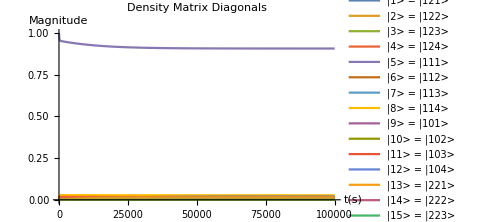
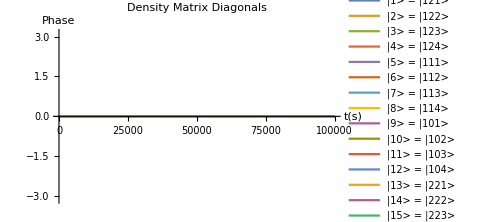

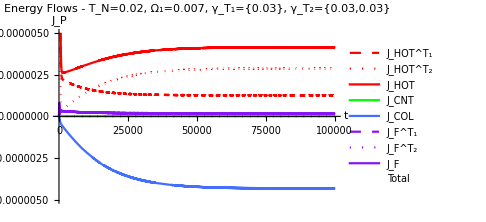

```mathematica
tmax=(100000/ωconv)//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,16Ns},{j,1,16Ns}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,16Ns}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {-π,π},
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->Table[StringForm["|``> = |``````>",i,EmapT1[i],Ns-EmapED[i],EmapT2[i]],{i,1,16Ns}]
]}

Flatten[{
Subscript[EngyFlowIn, 1,1][ρMatrix[t]],Subscript[EngyFlowIn, 1,2][ρMatrix[t]],Subscript[EngyFlowIn, 1,1][ρMatrix[t]]+Subscript[EngyFlowIn, 1,2][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 3][ρMatrix[t]],
Subscript[EngyFlowIn, 4,1][ρMatrix[t]],Subscript[EngyFlowIn, 4,2][ρMatrix[t]],Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]],
Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]+Subscript[EngyFlowIn, 3][ρMatrix[t]]+Subscript[EngyFlowIn, 4,1][ρMatrix[t]]+Subscript[EngyFlowIn, 4,2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style[StringForm["Energy Flows - T_N=``, Ω_1=``, 
γ_T_1=``, γ_T_2=``",Subscript[T, 2],Subscript[Ω, 1],Table[γT1[i],{i,0,Ns-1-p}],Table[γT2[i],{i,0,Ns-1-q}]]/.Flatten[{γassum,Tassum}]],
	PlotRange->{Automatic, {-0.5 10^-3 Econv Subscript[κ, 1]/.Tassum,0.5 10^-3 Econv Subscript[κ, 1]/.Tassum}},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"J_HOT^T_1","J_HOT^T_2","J_HOT","J_CNT","J_COL","J_F^T_1","J_F^T_2","J_F","Total"},
	PlotStyle->{{Red,Dashed},{Red,Dotted},Red,Green,BlueC,{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}}]
```

## Density matrices of the subsystems

Functions for taking the partial trace for the different subsystems. Here nL, nM, nR are the dimensionalities of the respective subsystems.

```mathematica
PartialTraceT1[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapT1[i]b,EmapT1[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nL,(nL nM nR)/nL}]]
,{a,1,nL},{b,1,nL}]
]
PartialTraceED[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapED[i]b,EmapED[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nM,(nL nM nR)/nM}]]
,{a,1,nM},{b,1,nM}]
]
PartialTraceT2[ρ_,nL_,nM_,nR_]:=Module[{temp0},
Table[
Tr[ArrayReshape[Pick[ρ,Table[a,EmapT2[i]b,EmapT2[j],{i,1,nL nM nR},{j,1,nL nM nR}],1],{(nL nM nR)/nR,(nL nM nR)/nR}]]
,{a,1,nR},{b,1,nR}]
]
```

```mathematica
PartialTraceT1[ρMatrix[t],4,Ns,4]//MatrixForm
PartialTraceED[ρMatrix[t],4,Ns,4]//MatrixForm
PartialTraceT2[ρMatrix[t],4,Ns,4]//MatrixForm
```

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(5,5)[t]+ρ_(6,6)[t]+ρ_(7,7)[t]+ρ_(8,8)[t]+ρ_(9,9)[t]+ρ_(10,10)[t]+ρ_(11,11)[t]+ρ_(12,12)[t] | ρ_(1,13)[t]+ρ_(2,14)[t]+ρ_(3,15)[t]+ρ_(4,16)[t]+ρ_(5,17)[t]+ρ_(6,18)[t]+ρ_(7,19)[t]+ρ_(8,20)[t]+ρ_(9,21)[t]+ρ_(10,22)[t]+ρ_(11,23)[t]+ρ_(12,24)[t] | ρ_(1,25)[t]+ρ_(2,26)[t]+ρ_(3,27)[t]+ρ_(4,28)[t]+ρ_(5,29)[t]+ρ_(6,30)[t]+ρ_(7,31)[t]+ρ_(8,32)[t]+ρ_(9,33)[t]+ρ_(10,34)[t]+ρ_(11,35)[t]+ρ_(12,36)[t] | ρ_(1,37)[t]+ρ_(2,38)[t]+ρ_(3,39)[t]+ρ_(4,40)[t]+ρ_(5,41)[t]+ρ_(6,42)[t]+ρ_(7,43)[t]+ρ_(8,44)[t]+ρ_(9,45)[t]+ρ_(10,46)[t]+ρ_(11,47)[t]+ρ_(12,48)[t]
ρ_(13,1)[t]+ρ_(14,2)[t]+ρ_(15,3)[t]+ρ_(16,4)[t]+ρ_(17,5)[t]+ρ_(18,6)[t]+ρ_(19,7)[t]+ρ_(20,8)[t]+ρ_(21,9)[t]+ρ_(22,10)[t]+ρ_(23,11)[t]+ρ_(24,12)[t] | ρ_(13,13)[t]+ρ_(14,14)[t]+ρ_(15,15)[t]+ρ_(16,16)[t]+ρ_(17,17)[t]+ρ_(18,18)[t]+ρ_(19,19)[t]+ρ_(20,20)[t]+ρ_(21,21)[t]+ρ_(22,22)[t]+ρ_(23,23)[t]+ρ_(24,24)[t] | ρ_(13,25)[t]+ρ_(14,26)[t]+ρ_(15,27)[t]+ρ_(16,28)[t]+ρ_(17,29)[t]+ρ_(18,30)[t]+ρ_(19,31)[t]+ρ_(20,32)[t]+ρ_(21,33)[t]+ρ_(22,34)[t]+ρ_(23,35)[t]+ρ_(24,36)[t] | ρ_(13,37)[t]+ρ_(14,38)[t]+ρ_(15,39)[t]+ρ_(16,40)[t]+ρ_(17,41)[t]+ρ_(18,42)[t]+ρ_(19,43)[t]+ρ_(20,44)[t]+ρ_(21,45)[t]+ρ_(22,46)[t]+ρ_(23,47)[t]+ρ_(24,48)[t]
ρ_(25,1)[t]+ρ_(26,2)[t]+ρ_(27,3)[t]+ρ_(28,4)[t]+ρ_(29,5)[t]+ρ_(30,6)[t]+ρ_(31,7)[t]+ρ_(32,8)[t]+ρ_(33,9)[t]+ρ_(34,10)[t]+ρ_(35,11)[t]+ρ_(36,12)[t] | ρ_(25,13)[t]+ρ_(26,14)[t]+ρ_(27,15)[t]+ρ_(28,16)[t]+ρ_(29,17)[t]+ρ_(30,18)[t]+ρ_(31,19)[t]+ρ_(32,20)[t]+ρ_(33,21)[t]+ρ_(34,22)[t]+ρ_(35,23)[t]+ρ_(36,24)[t] | ρ_(25,25)[t]+ρ_(26,26)[t]+ρ_(27,27)[t]+ρ_(28,28)[t]+ρ_(29,29)[t]+ρ_(30,30)[t]+ρ_(31,31)[t]+ρ_(32,32)[t]+ρ_(33,33)[t]+ρ_(34,34)[t]+ρ_(35,35)[t]+ρ_(36,36)[t] | ρ_(25,37)[t]+ρ_(26,38)[t]+ρ_(27,39)[t]+ρ_(28,40)[t]+ρ_(29,41)[t]+ρ_(30,42)[t]+ρ_(31,43)[t]+ρ_(32,44)[t]+ρ_(33,45)[t]+ρ_(34,46)[t]+ρ_(35,47)[t]+ρ_(36,48)[t]
ρ_(37,1)[t]+ρ_(38,2)[t]+ρ_(39,3)[t]+ρ_(40,4)[t]+ρ_(41,5)[t]+ρ_(42,6)[t]+ρ_(43,7)[t]+ρ_(44,8)[t]+ρ_(45,9)[t]+ρ_(46,10)[t]+ρ_(47,11)[t]+ρ_(48,12)[t] | ρ_(37,13)[t]+ρ_(38,14)[t]+ρ_(39,15)[t]+ρ_(40,16)[t]+ρ_(41,17)[t]+ρ_(42,18)[t]+ρ_(43,19)[t]+ρ_(44,20)[t]+ρ_(45,21)[t]+ρ_(46,22)[t]+ρ_(47,23)[t]+ρ_(48,24)[t] | ρ_(37,25)[t]+ρ_(38,26)[t]+ρ_(39,27)[t]+ρ_(40,28)[t]+ρ_(41,29)[t]+ρ_(42,30)[t]+ρ_(43,31)[t]+ρ_(44,32)[t]+ρ_(45,33)[t]+ρ_(46,34)[t]+ρ_(47,35)[t]+ρ_(48,36)[t] | ρ_(37,37)[t]+ρ_(38,38)[t]+ρ_(39,39)[t]+ρ_(40,40)[t]+ρ_(41,41)[t]+ρ_(42,42)[t]+ρ_(43,43)[t]+ρ_(44,44)[t]+ρ_(45,45)[t]+ρ_(46,46)[t]+ρ_(47,47)[t]+ρ_(48,48)[t])

(ρ_(1,1)[t]+ρ_(2,2)[t]+ρ_(3,3)[t]+ρ_(4,4)[t]+ρ_(13,13)[t]+ρ_(14,14)[t]+ρ_(15,15)[t]+ρ_(16,16)[t]+ρ_(25,25)[t]+ρ_(26,26)[t]+ρ_(27,27)[t]+ρ_(28,28)[t]+ρ_(37,37)[t]+ρ_(38,38)[t]+ρ_(39,39)[t]+ρ_(40,40)[t] | ρ_(1,5)[t]+ρ_(2,6)[t]+ρ_(3,7)[t]+ρ_(4,8)[t]+ρ_(13,17)[t]+ρ_(14,18)[t]+ρ_(15,19)[t]+ρ_(16,20)[t]+ρ_(25,29)[t]+ρ_(26,30)[t]+ρ_(27,31)[t]+ρ_(28,32)[t]+ρ_(37,41)[t]+ρ_(38,42)[t]+ρ_(39,43)[t]+ρ_(40,44)[t] | ρ_(1,9)[t]+ρ_(2,10)[t]+ρ_(3,11)[t]+ρ_(4,12)[t]+ρ_(13,21)[t]+ρ_(14,22)[t]+ρ_(15,23)[t]+ρ_(16,24)[t]+ρ_(25,33)[t]+ρ_(26,34)[t]+ρ_(27,35)[t]+ρ_(28,36)[t]+ρ_(37,45)[t]+ρ_(38,46)[t]+ρ_(39,47)[t]+ρ_(40,48)[t]
ρ_(5,1)[t]+ρ_(6,2)[t]+ρ_(7,3)[t]+ρ_(8,4)[t]+ρ_(17,13)[t]+ρ_(18,14)[t]+ρ_(19,15)[t]+ρ_(20,16)[t]+ρ_(29,25)[t]+ρ_(30,26)[t]+ρ_(31,27)[t]+ρ_(32,28)[t]+ρ_(41,37)[t]+ρ_(42,38)[t]+ρ_(43,39)[t]+ρ_(44,40)[t] | ρ_(5,5)[t]+ρ_(6,6)[t]+ρ_(7,7)[t]+ρ_(8,8)[t]+ρ_(17,17)[t]+ρ_(18,18)[t]+ρ_(19,19)[t]+ρ_(20,20)[t]+ρ_(29,29)[t]+ρ_(30,30)[t]+ρ_(31,31)[t]+ρ_(32,32)[t]+ρ_(41,41)[t]+ρ_(42,42)[t]+ρ_(43,43)[t]+ρ_(44,44)[t] | ρ_(5,9)[t]+ρ_(6,10)[t]+ρ_(7,11)[t]+ρ_(8,12)[t]+ρ_(17,21)[t]+ρ_(18,22)[t]+ρ_(19,23)[t]+ρ_(20,24)[t]+ρ_(29,33)[t]+ρ_(30,34)[t]+ρ_(31,35)[t]+ρ_(32,36)[t]+ρ_(41,45)[t]+ρ_(42,46)[t]+ρ_(43,47)[t]+ρ_(44,48)[t]
ρ_(9,1)[t]+ρ_(10,2)[t]+ρ_(11,3)[t]+ρ_(12,4)[t]+ρ_(21,13)[t]+ρ_(22,14)[t]+ρ_(23,15)[t]+ρ_(24,16)[t]+ρ_(33,25)[t]+ρ_(34,26)[t]+ρ_(35,27)[t]+ρ_(36,28)[t]+ρ_(45,37)[t]+ρ_(46,38)[t]+ρ_(47,39)[t]+ρ_(48,40)[t] | ρ_(9,5)[t]+ρ_(10,6)[t]+ρ_(11,7)[t]+ρ_(12,8)[t]+ρ_(21,17)[t]+ρ_(22,18)[t]+ρ_(23,19)[t]+ρ_(24,20)[t]+ρ_(33,29)[t]+ρ_(34,30)[t]+ρ_(35,31)[t]+ρ_(36,32)[t]+ρ_(45,41)[t]+ρ_(46,42)[t]+ρ_(47,43)[t]+ρ_(48,44)[t] | ρ_(9,9)[t]+ρ_(10,10)[t]+ρ_(11,11)[t]+ρ_(12,12)[t]+ρ_(21,21)[t]+ρ_(22,22)[t]+ρ_(23,23)[t]+ρ_(24,24)[t]+ρ_(33,33)[t]+ρ_(34,34)[t]+ρ_(35,35)[t]+ρ_(36,36)[t]+ρ_(45,45)[t]+ρ_(46,46)[t]+ρ_(47,47)[t]+ρ_(48,48)[t])

(ρ_(1,1)[t]+ρ_(5,5)[t]+ρ_(9,9)[t]+ρ_(13,13)[t]+ρ_(17,17)[t]+ρ_(21,21)[t]+ρ_(25,25)[t]+ρ_(29,29)[t]+ρ_(33,33)[t]+ρ_(37,37)[t]+ρ_(41,41)[t]+ρ_(45,45)[t] | ρ_(1,2)[t]+ρ_(5,6)[t]+ρ_(9,10)[t]+ρ_(13,14)[t]+ρ_(17,18)[t]+ρ_(21,22)[t]+ρ_(25,26)[t]+ρ_(29,30)[t]+ρ_(33,34)[t]+ρ_(37,38)[t]+ρ_(41,42)[t]+ρ_(45,46)[t] | ρ_(1,3)[t]+ρ_(5,7)[t]+ρ_(9,11)[t]+ρ_(13,15)[t]+ρ_(17,19)[t]+ρ_(21,23)[t]+ρ_(25,27)[t]+ρ_(29,31)[t]+ρ_(33,35)[t]+ρ_(37,39)[t]+ρ_(41,43)[t]+ρ_(45,47)[t] | ρ_(1,4)[t]+ρ_(5,8)[t]+ρ_(9,12)[t]+ρ_(13,16)[t]+ρ_(17,20)[t]+ρ_(21,24)[t]+ρ_(25,28)[t]+ρ_(29,32)[t]+ρ_(33,36)[t]+ρ_(37,40)[t]+ρ_(41,44)[t]+ρ_(45,48)[t]
ρ_(2,1)[t]+ρ_(6,5)[t]+ρ_(10,9)[t]+ρ_(14,13)[t]+ρ_(18,17)[t]+ρ_(22,21)[t]+ρ_(26,25)[t]+ρ_(30,29)[t]+ρ_(34,33)[t]+ρ_(38,37)[t]+ρ_(42,41)[t]+ρ_(46,45)[t] | ρ_(2,2)[t]+ρ_(6,6)[t]+ρ_(10,10)[t]+ρ_(14,14)[t]+ρ_(18,18)[t]+ρ_(22,22)[t]+ρ_(26,26)[t]+ρ_(30,30)[t]+ρ_(34,34)[t]+ρ_(38,38)[t]+ρ_(42,42)[t]+ρ_(46,46)[t] | ρ_(2,3)[t]+ρ_(6,7)[t]+ρ_(10,11)[t]+ρ_(14,15)[t]+ρ_(18,19)[t]+ρ_(22,23)[t]+ρ_(26,27)[t]+ρ_(30,31)[t]+ρ_(34,35)[t]+ρ_(38,39)[t]+ρ_(42,43)[t]+ρ_(46,47)[t] | ρ_(2,4)[t]+ρ_(6,8)[t]+ρ_(10,12)[t]+ρ_(14,16)[t]+ρ_(18,20)[t]+ρ_(22,24)[t]+ρ_(26,28)[t]+ρ_(30,32)[t]+ρ_(34,36)[t]+ρ_(38,40)[t]+ρ_(42,44)[t]+ρ_(46,48)[t]
ρ_(3,1)[t]+ρ_(7,5)[t]+ρ_(11,9)[t]+ρ_(15,13)[t]+ρ_(19,17)[t]+ρ_(23,21)[t]+ρ_(27,25)[t]+ρ_(31,29)[t]+ρ_(35,33)[t]+ρ_(39,37)[t]+ρ_(43,41)[t]+ρ_(47,45)[t] | ρ_(3,2)[t]+ρ_(7,6)[t]+ρ_(11,10)[t]+ρ_(15,14)[t]+ρ_(19,18)[t]+ρ_(23,22)[t]+ρ_(27,26)[t]+ρ_(31,30)[t]+ρ_(35,34)[t]+ρ_(39,38)[t]+ρ_(43,42)[t]+ρ_(47,46)[t] | ρ_(3,3)[t]+ρ_(7,7)[t]+ρ_(11,11)[t]+ρ_(15,15)[t]+ρ_(19,19)[t]+ρ_(23,23)[t]+ρ_(27,27)[t]+ρ_(31,31)[t]+ρ_(35,35)[t]+ρ_(39,39)[t]+ρ_(43,43)[t]+ρ_(47,47)[t] | ρ_(3,4)[t]+ρ_(7,8)[t]+ρ_(11,12)[t]+ρ_(15,16)[t]+ρ_(19,20)[t]+ρ_(23,24)[t]+ρ_(27,28)[t]+ρ_(31,32)[t]+ρ_(35,36)[t]+ρ_(39,40)[t]+ρ_(43,44)[t]+ρ_(47,48)[t]
ρ_(4,1)[t]+ρ_(8,5)[t]+ρ_(12,9)[t]+ρ_(16,13)[t]+ρ_(20,17)[t]+ρ_(24,21)[t]+ρ_(28,25)[t]+ρ_(32,29)[t]+ρ_(36,33)[t]+ρ_(40,37)[t]+ρ_(44,41)[t]+ρ_(48,45)[t] | ρ_(4,2)[t]+ρ_(8,6)[t]+ρ_(12,10)[t]+ρ_(16,14)[t]+ρ_(20,18)[t]+ρ_(24,22)[t]+ρ_(28,26)[t]+ρ_(32,30)[t]+ρ_(36,34)[t]+ρ_(40,38)[t]+ρ_(44,42)[t]+ρ_(48,46)[t] | ρ_(4,3)[t]+ρ_(8,7)[t]+ρ_(12,11)[t]+ρ_(16,15)[t]+ρ_(20,19)[t]+ρ_(24,23)[t]+ρ_(28,27)[t]+ρ_(32,31)[t]+ρ_(36,35)[t]+ρ_(40,39)[t]+ρ_(44,43)[t]+ρ_(48,47)[t] | ρ_(4,4)[t]+ρ_(8,8)[t]+ρ_(12,12)[t]+ρ_(16,16)[t]+ρ_(20,20)[t]+ρ_(24,24)[t]+ρ_(28,28)[t]+ρ_(32,32)[t]+ρ_(36,36)[t]+ρ_(40,40)[t]+ρ_(44,44)[t]+ρ_(48,48)[t])

## Numerically obtaining the approximate steady-state

Because ParallelTable doesn’t work properly with EngyFlowIn_P[ρ], we need to redefine them

```mathematica
EngyFlowInHT1=Subscript[EngyFlowIn, 1,1][ρMatrix[t]];
EngyFlowInHT2=Subscript[EngyFlowIn, 1,2][ρMatrix[t]];
EngyFlowInN=Subscript[EngyFlowIn, 2][ρMatrix[t]];
EngyFlowInC=Subscript[EngyFlowIn, 3][ρMatrix[t]];
EngyFlowInFT1=Subscript[EngyFlowIn, 4,1][ρMatrix[t]];
EngyFlowInFT2=Subscript[EngyFlowIn, 4,2][ρMatrix[t]];
```

```mathematica
varFunc[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,groundstate 1,{i,1,16Ns},{j,1,16Ns}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,16Ns}]/.temp2]],
Re[Flatten[{
EngyFlowInHT1,EngyFlowInHT2,EngyFlowInHT1+EngyFlowInHT2,EngyFlowInN,EngyFlowInC,
EngyFlowInFT1,EngyFlowInFT2,EngyFlowInFT1+EngyFlowInFT2,
EngyFlowInHT1+EngyFlowInHT2+EngyFlowInN+EngyFlowInC+EngyFlowInFT1+EngyFlowInFT2}//.Flatten[{t->tmax,temp0}]/.temp2]],
Table[Subscript[ρ, i,j][tmax],{i,1,16Ns},{j,1,16Ns}]/.temp2
}
]
```

```mathematica
varFunc[0.2,0.10,0.02,0.01,0.01,0.01,0.7,0.8,0.8,1.2,0.4,0.0,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],100000,unitassum][[1;;2]]//AbsoluteTiming
```

{8.54394,{{2.09199×10^-14,4.10502×10^-9,4.61038×10^-7,1.51447×10^-12,2.52118×10^-11,7.98628×10^-9,1.04008×10^-6,3.2737×10^-9,3.41646×10^-11,1.50126×10^-6,0.00011911,4.72884×10^-9,5.22855×10^-11,1.8351×10^-6,0.000145643,5.42655×10^-9,1.2146×10^-8,2.73466×10^-6,0.000323933,1.45165×10^-6,1.5788×10^-8,0.000500303,0.0275978,2.1454×10^-6,3.77373×10^-9,0.000110368,0.0085278,4.32412×10^-7,5.44187×10^-7,0.000092213,0.0108623,0.0000736675,5.36582×10^-7,0.0169505,0.925831,0.0000724528,2.94983×10^-12,4.26837×10^-7,0.0000469782,2.28908×10^-10,2.64737×10^-9,8.03681×10^-7,0.000106025,3.4073×10^-7,2.58461×10^-9,0.000104581,0.00852101,3.96873×10^-7},{3.19718×10^-6,1.45938×10^-6,4.65656×10^-6,-2.46737×10^-6,-2.18907×10^-6,0.,0.,0.,1.19285×10^-10}}}

```mathematica
varFunc[T1_,T2_,T3_,κ1_,κ2_,κ3_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1_,Ω2_,γT1s_,γT2s_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[T, 3]->T3,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[κ, 3]->κ3,Subscript[Ω, 1]->Ω1,Subscript[Ω, 2]->Ω2,Subscript[ωLM, 1]->ωLM1,Subscript[ωMR, 1]->ωMR1,Subscript[ωLM, 2]->ωLM2,Subscript[ωMR, 2]->ωMR2,ωED->ωEDs,Table[γT1[i]->γT1s[[i+1]],{i,0,Ns-1-p}],Table[γT2[i]->γT2s[[i+1]],{i,0,Ns-1-q}]}];
temp1=sol//.temp0;
temp2=NSolve[Flatten[{temp1//.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},∑_(i=1)^(16 Ns) Subscript[ρ, i,i]==1}],Flatten[Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]]];
temp3=Table[Subscript[ρ, i,j],{i,1,16Ns},{j,1,16Ns}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i],{i,1,16Ns}]/.temp2]],
Re[Flatten[{
EngyFlowInHT1,EngyFlowInHT2,EngyFlowInHT1+EngyFlowInHT2,EngyFlowInN,EngyFlowInC,
EngyFlowInFT1,EngyFlowInFT2,EngyFlowInFT1+EngyFlowInFT2,
EngyFlowInHT1+EngyFlowInHT2+EngyFlowInN+EngyFlowInC+EngyFlowInFT1+EngyFlowInFT2}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp2]],
PartialTraceT1[temp3,4,Ns,4],
PartialTraceED[temp3,4,Ns,4],
PartialTraceT2[temp3,4,Ns,4],
Diagonal[Re[PartialTraceT1[temp3,4,Ns,4]]],
Diagonal[Re[PartialTraceED[temp3,4,Ns,4]]],
Diagonal[Re[PartialTraceT2[temp3,4,Ns,4]]]
}
]
```

```mathematica
varFunc[0.2,0.10,0.02,0.01,0.01,0.01,0.7,0.8,0.8,1.2,0.4,0.0,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],unitassum]//AbsoluteTiming
```

{2.429,{{2.09263×10^-14,4.105×10^-9,4.61036×10^-7,1.515×10^-12,2.52117×10^-11,7.98899×10^-9,1.04044×10^-6,3.27368×10^-9,3.41762×10^-11,1.50125×10^-6,0.000119109,4.73045×10^-9,5.23033×10^-11,1.83509×10^-6,0.000145643,5.4284×10^-9,1.2146×10^-8,2.73557×10^-6,0.00032404,1.45164×10^-6,1.57933×10^-8,0.000500301,0.0275977,2.14611×10^-6,3.77501×10^-9,0.000110368,0.00852777,4.3256×10^-7,5.44184×10^-7,0.0000922434,0.0108659,0.0000736672,5.3676×10^-7,0.0169504,0.925827,0.0000724767,2.95085×10^-12,4.26836×10^-7,0.000046978,2.28987×10^-10,2.64736×10^-9,8.03954×10^-7,0.000106061,3.40728×10^-7,2.58549×10^-9,0.000104581,0.00852098,3.97007×10^-7},{3.19717×10^-6,1.45962×10^-6,4.65679×10^-6,-2.46736×10^-6,-2.18943×10^-6,0.,0.,0.,-1.53847×10^-17},{{0.000122132+0. ⅈ,0,0,0},{0,0.0285759+0. ⅈ,0,0},{0,0,0.962521+0. ⅈ,0},{0,0,0,0.00878057+0. ⅈ}},{{0.00883393+0. ⅈ,0,0},{0,0.0114688+0. ⅈ,0},{0,0,0.979697+0. ⅈ}},{{1.11801×10^-6+0. ⅈ,0,0.,0},{0,0.0177652+0. ⅈ,0,0},{0.,0,0.982083+0. ⅈ,0},{0,0,0,0.000150926+0. ⅈ}},{0.000122132,0.0285759,0.962521,0.00878057},{0.00883393,0.0114688,0.979697},{1.11801×10^-6,0.0177652,0.982083,0.000150926}}}

Some example configurations

{1.21021×10^-6,2.42043×10^-6,3.63064×10^-6,0.,-3.63064×10^-6,6.05107×10^-7,0.,6.05107×10^-7,6.05107×10^-7}

{(0.00026193+0. ⅈ | 0 | 0 | 0
0 | 0.017542+0. ⅈ | 0 | 0.-0.00021611 ⅈ
0 | 0 | 0.967783+0. ⅈ | 0
0 | 0.+0.00021611 ⅈ | 0 | 0.0144129+0. ⅈ),(0.0145171+0. ⅈ | 0 | 0
0 | 0.0189986+0. ⅈ | 0
0 | 0 | 0.966484+0. ⅈ),(1.85394×10^-6+0. ⅈ | 0 | 0 | 0
0 | 0.0176198+0. ⅈ | 0 | 0
0 | 0 | 0.982128+0. ⅈ | 0
0 | 0 | 0 | 0.000250274+0. ⅈ)}

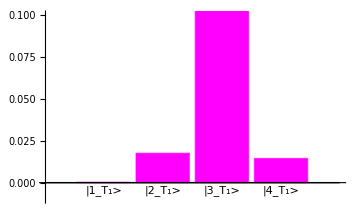
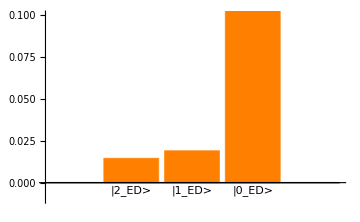
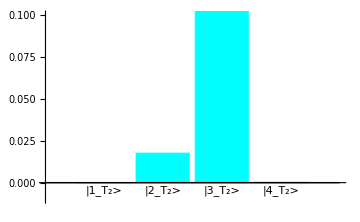

```mathematica
temp=varFunc[0.2,0.02,0.02,0.01,0.00,0.01,0.8,1.2,0.8,1.2,0.40,0.007,0.0,ConstantArray[0.015ωconv,Ns-p],ConstantArray[0.015ωconv,Ns-q],unitassum];
temp[[2]]
{temp[[3]]//MatrixForm,temp[[4]]//MatrixForm,temp[[5]]//MatrixForm}
{BarChart[temp[[6]],ChartLabels->{"|1_T_1>","|2_T_1>","|3_T_1>","|4_T_1>"},ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Magenta],
BarChart[temp[[7]],ChartLabels->{"|2_ED>","|1_ED>","|0_ED>"},ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Orange],
BarChart[temp[[8]],ChartLabels->{"|1_T_2>","|2_T_2>","|3_T_2>","|4_T_2>"},ImageSize->Medium,PlotRange->{-0.01,0.1},ChartStyle->Cyan]}
```

## Energy flow characteristics for different system parameters

### Energy flow under different control temperatures

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithTcnt[Thot_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω1s_,Ω2s_,γT1s_,γT2s_,Tcntmin_,Tcntmax_,Tres_,legends_,title_]:=Module[{tempx,tempy,combflows,denmatT1,denmatED,denmatT2},
tempx=Table[Tcnt/Thot,{Tcnt,Tcntmin,Tcntmax,Tres},{i,1,9}];
tempy=ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1s,Ω2s,γT1s,γT2s,unitassum],{Tcnt,Tcntmin,Tcntmax,Tres}];
combflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,2,i]]}],{i,1,9}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,6,i]]}],{i,1,4}];
denmatED=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,7,i]]}],{i,1,3}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,8,i]]}],{i,1,4}];
{ListPlot[combflows,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},Full},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red,Dashed},{Red,Dotted},{Red},{Green},{BlueC},{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}},
PlotLegends->legends &&{
Style["J_H^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["Total",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT1,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatED,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["ED - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|2_ED>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|1_ED>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|0_ED>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT2,
PlotRange->{{Tcntmin/Thot,Tcntmax/Thot},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["T_N/T_H",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}]
}
]
```

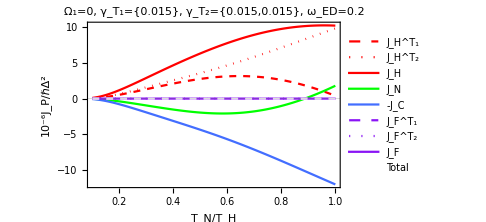
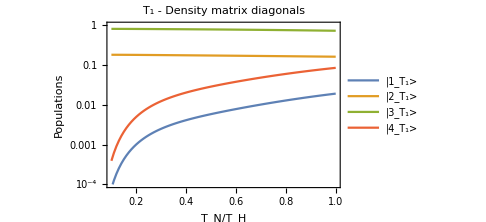
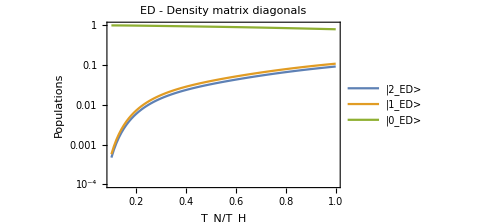
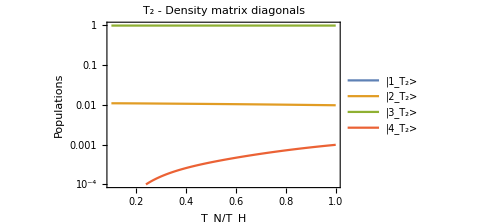

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;
ωLM2=0.9ωconv;ωMR2=1.1ωconv;
ωEDs=0.2ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,True,StringForm["Ω_1=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Ω1,γT1s,γT2s,ωEDs]]
]
```

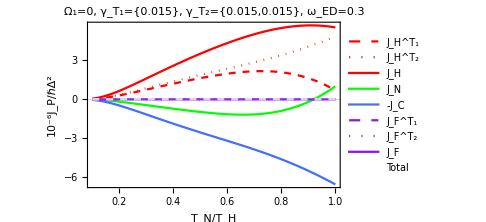
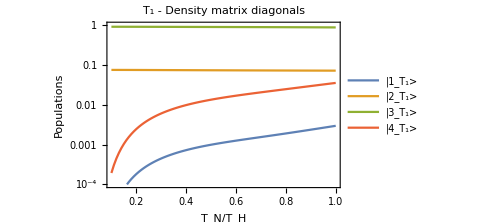
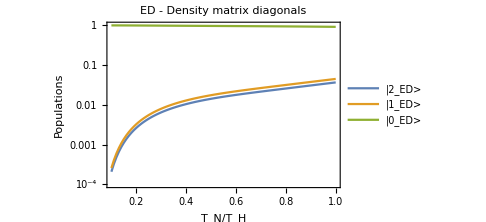
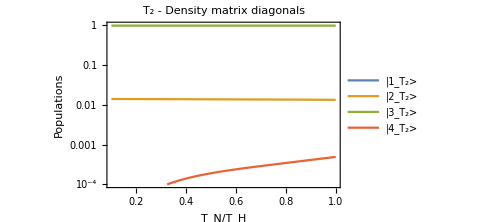

```mathematica
Module[{Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres},
Thot=0.2Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.001;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;
ωLM2=0.85ωconv;ωMR2=1.15ωconv;
ωEDs=0.3ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω1=0ωconv;Ω2=0ωconv;
Tcntmin=0.02Tconv;Tcntmax=0.20Tconv;Tres=0.002Tconv;
PlotEngyFlowsWithTcnt[Thot,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2,γT1s,γT2s,Tcntmin,Tcntmax,Tres,True,StringForm["Ω_1=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Ω1,γT1s,γT2s,ωEDs]]
]
```

### Energy flow under different field strengths

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping the γs constant,

```mathematica
PlotEngyFlowsWithΩ1[Thot_,Tcnt_,Tcol_,κhot_,κcnt_,κcol_,ωLM1_,ωMR1_,ωLM2_,ωMR2_,ωEDs_,Ω2s_,γT1s_,γT2s_,Ω1min_,Ω1max_,Ωres_,legends_,title_]:=Module[{tempx,tempy,combflows,denmatT1,denmatED,denmatT2},
tempx=Table[Ω1/(κhot ωconv),{Ω1,Ω1min,Ω1max,Ωres},{i,1,9}];
tempy=ParallelTable[varFunc[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω1,Ω2s,γT1s,γT2s,unitassum],{Ω1,Ω1min,Ω1max,Ωres}];
combflows=Table[MapThread[List,{tempx[[;;,i]],10^6 tempy[[;;,2,i]]}],{i,1,9}];
denmatT1=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,6,i]]}],{i,1,4}];
denmatED=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,7,i]]}],{i,1,3}];
denmatT2=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,8,i]]}],{i,1,4}];
{ListPlot[combflows,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},Full},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["10^-6J_P/ℏΔ^2",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
PlotStyle->{{Red,Dashed},{Red,Dotted},{Red},{Green},{BlueC},{PurpleC,Dashed},{PurpleC,Dotted},PurpleC,{White,Dashed}},
PlotLegends->legends &&{
Style["J_H^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_H",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_N",FontFamily->"Times New Roman",FontSize->14.5],
Style["-J_C",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_1",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F^T_2",FontFamily->"Times New Roman",FontSize->14.5],
Style["J_F",FontFamily->"Times New Roman",FontSize->14.5],
Style["Total",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT1,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_1 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_1>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_1>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatED,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["ED - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|2_ED>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|1_ED>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|0_ED>",FontFamily->"Times New Roman",FontSize->14.5]}],
ListLogPlot[denmatT2,
PlotRange->{{Ω1min/(κhot ωconv),Ω1max/(κhot ωconv)},{0.0001,1}},
ImageSize->Medium,
Axes->False,
Frame-> {{True,False},{True,False}},
FrameLabel->{
		Style["Ω_F/κΔ",FontFamily->"Times New Roman",FontSize->15],
		Style["Populations",FontFamily->"Times New Roman",FontSize->15]},
FrameStyle->Directive[Darker[Gray],14,FontFamily->"Times New Roman"],
GridLines->{None,{0}},
Joined->True,
PlotLabel->Style["T_2 - Density matrix diagonals",FontFamily->"Times New Roman",FontSize->14.5],
PlotLegends->legends &&{
Style["|1_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|2_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|3_T_2>",FontFamily->"Times New Roman",FontSize->14.5],
Style["|4_T_2>",FontFamily->"Times New Roman",FontSize->14.5]}]
}
]
```

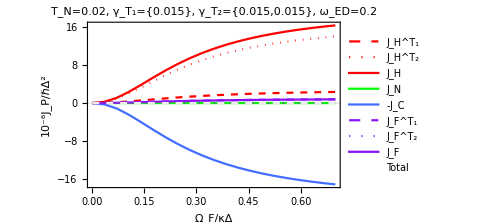
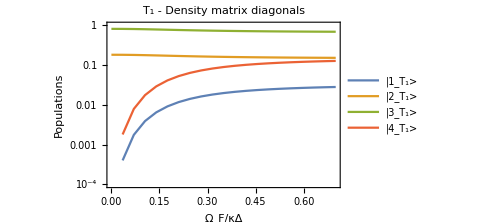
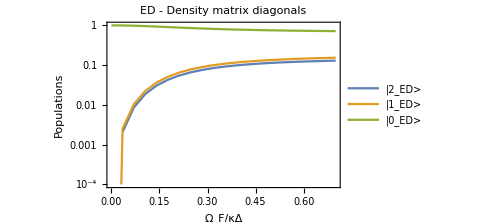
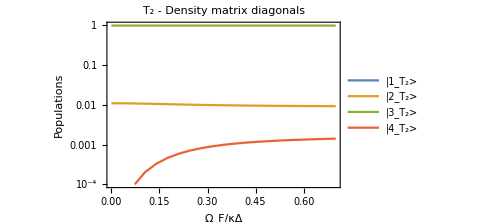

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.3ωconv;ωMR1=0.4ωconv;ωLM2=0.9ωconv;ωMR2=1.1ωconv;ωEDs=0.2ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00035ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
]
```

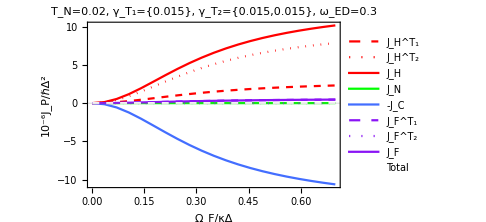
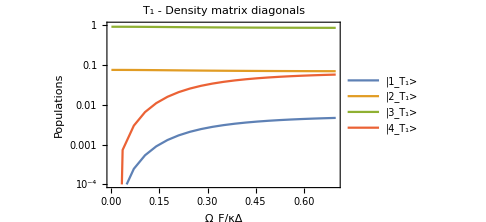
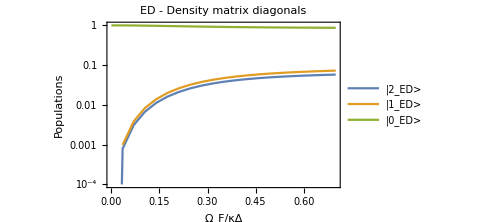
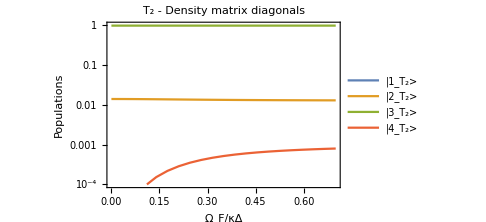

```mathematica
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.00;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=0.85ωconv;ωMR2=1.15ωconv;ωEDs=0.3ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.00035ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
]
```

#### For different energy divider coupling strengths

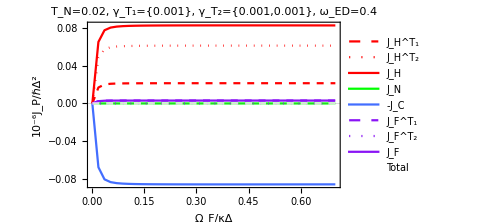
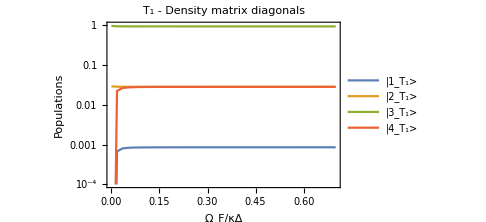
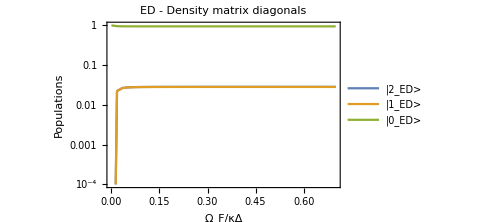
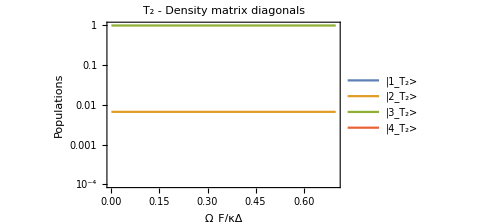
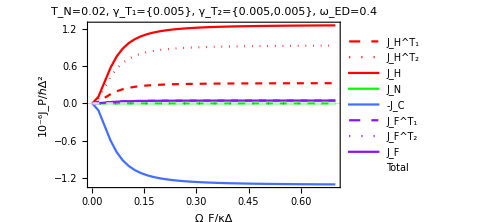
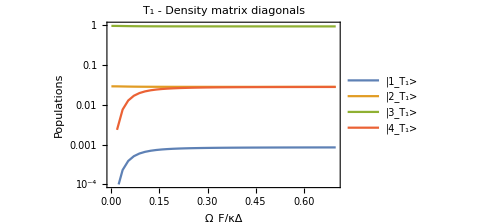
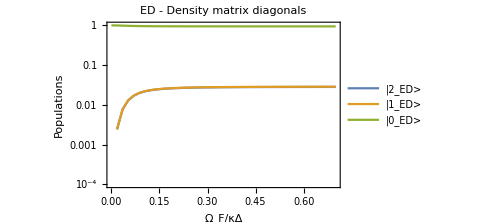
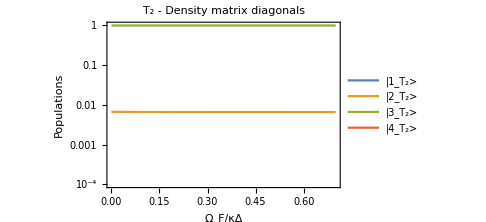

```mathematica
{
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.5ωconv;ωMR1=0.6ωconv;ωLM2=1.0ωconv;ωMR2=1.3ωconv;ωEDs=0.3ωconv;
γT1s={0.001ωconv};
γT2s={0.001ωconv,0.001ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.005ωconv};
γT2s={0.005ωconv,0.005ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.010ωconv};
γT2s={0.010ωconv,0.010ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.015ωconv};
γT2s={0.015ωconv,0.015ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.025ωconv};
γT2s={0.025ωconv,0.025ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.050ωconv};
γT2s={0.050ωconv,0.050ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
],
Module[{Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res},
Thot=0.2Tconv;Tcnt=0.02Tconv;Tcol=0.02Tconv;
κhot=0.01;κcnt=0.0;κcol=0.01;
ωLM1=0.7ωconv;ωMR1=0.8ωconv;ωLM2=1.0ωconv;ωMR2=1.4ωconv;ωEDs=0.40ωconv;
γT1s={0.050ωconv};
γT2s={0.150ωconv,0.150ωconv};
Ω2=0ωconv;
Ω1min=0ωconv;Ω1max=0.007ωconv;Ω1res=0.000175ωconv;
PlotEngyFlowsWithΩ1[Thot,Tcnt,Tcol,κhot,κcnt,κcol,ωLM1,ωMR1,ωLM2,ωMR2,ωEDs,Ω2,γT1s,γT2s,Ω1min,Ω1max,Ω1res,True,StringForm["T_N=``, γ_T_1=``, γ_T_2=``, ω_ED=``",Tcnt,γT1s,γT2s,ωEDs]]
]
}
```